```mathematica
(*Exit[];*)
```

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&];
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];
```

```mathematica
temp=Import[NotebookDirectory[]<>"../output/yield-pi-plus-rn.dat","Table"];
```

```mathematica
Print[Take[temp,5]]
```

{{#,pT,phi_p,y_p,dNd3p,dNd3p,(GeV^{-3})},{0.,0.,-1.,0.172185,22.409631070595701},{0.,0.20944,-1.,0.172185,22.409631070595701},{0.,0.418879,-1.,0.172185,22.409631070595701},{0.,0.628319,-1.,0.172185,22.409631070595701}}

```mathematica
labels = First[temp][[2;;6]]
points=Rest[temp];
structuredData={#[[1;;3]],#[[5]]}&/@points;
Print[Take[structuredData,5]](*Print the first 5 structured data points*)


localYield=Interpolation[structuredData]
```

{pT,phi_p,y_p,dNd3p,dNd3p}

{{{0.,0.,-1.},22.409631070595701},{{0.,0.20944,-1.},22.409631070595701},{{0.,0.418879,-1.},22.409631070595701},{{0.,0.628319,-1.},22.409631070595701},{{0.,0.837758,-1.},22.409631070595701}}

```mathematica
Print[Take[points,5]]
```

{{0.,0.,-1.,0.172185,22.409631070595701},{0.,0.20944,-1.,0.172185,22.409631070595701},{0.,0.418879,-1.,0.172185,22.409631070595701},{0.,0.628319,-1.,0.172185,22.409631070595701},{0.,0.837758,-1.,0.172185,22.409631070595701}}

```mathematica
structuredData2={#[[1;;3]],#[[4]]}&/@points;
Print[Take[structuredData2,5]]
```

{{{0.,0.,-1.},0.172185},{{0.,0.20944,-1.},0.172185},{{0.,0.418879,-1.},0.172185},{{0.,0.628319,-1.},0.172185},{{0.,0.837758,-1.},0.172185}}

```mathematica
structuredData[[1]]
```

{{0.,0.,-1.},22.409631070595701}

```mathematica
localYield[0,0,-1]
```

22.4096

```mathematica
dNd3p[pT_,phi_,y_]:=localYield[pT,phi,y]
```

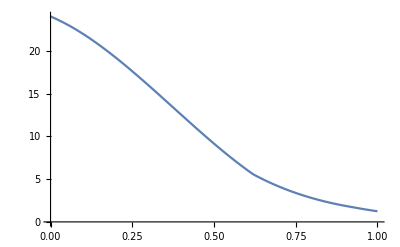

```mathematica
Plot[dNd3p[pT,0,0],{pT,0,1}]
```

```mathematica
vol=NIntegrate[dNd3p[pT,phi,y]pT^2,{phi,0,2Pi},{pT,0,6.2},{y,-1,1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
dNdy[y_]:=NIntegrate[dNd3p[pT,phi,y]pT^2,{phi,0,2Pi},{pT,0,6.2}]
```

```mathematica
dNdP[pT_]:=NIntegrate[dNd3p[pT,phi,y],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
vol
```

21.0134

```mathematica
dNdy[0.001]
```

19.993

```mathematica
dNdP[6]
```

1.09865×10^-7

```mathematica
yield1=Table[{pT,dNdP[pT]},{pT,0,6.2,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
yield2=Table[{y,dNdy[y]},{y,-1,1,0.01}];
```

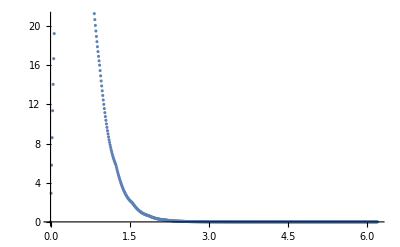

```mathematica
ListPlot[yield1,PlotRange->Automatic]
```

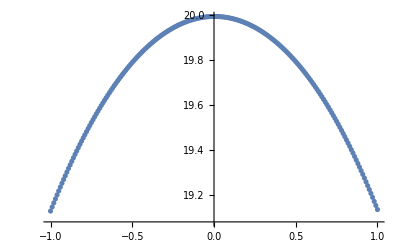

```mathematica
ListPlot[yield2]
```

```mathematica
yield3=Table[{y,dNdy[y]},{y,-.1,.1,0.01}];
```

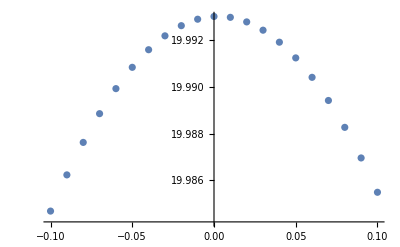

```mathematica
ListPlot[yield3]
```

```mathematica
v1[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Sin[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v2[pT_]:=1/vol NIntegrate[dNd3p[pT,phi,y]*Cos[phi],{phi,0,2Pi},{y,-1,1}]
```

```mathematica
v1list=Table[{pT,v1[pT]},{pT,0.01,3,0.1}];
```

```mathematica
v2list=Table[{pT,v2[pT]},{pT,0,3,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.27084×10^-14 and 1.76942×10^-13 for the integral and error estimates.

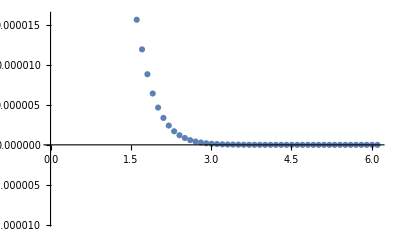

```mathematica
ListPlot[v1list]
```

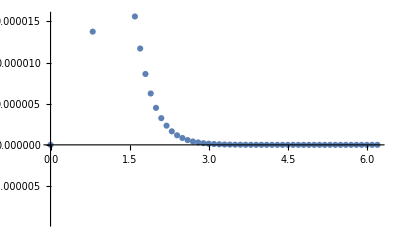

```mathematica
ListPlot[v2list]
```